# FourierBasis

## The discrete Fourier basis and the pair-plane

## Purpose

This notebook supports the Fourier-basis results of Chapter 1. It constructs the normalized discrete Fourier vectors, verifies orthonormality and completeness, computes Fourier coefficients, and illustrates the geometry of the pair-plane E_(±1).

All executable cells are ordinary Wolfram Language Input cells. Typeset box expressions are used only in explanatory cells.

## 1. Definitions

```mathematica
ClearAll["Global`*"];

omega[n_Integer?Positive] := Exp[2 Pi I/n];

fourierVector[n_Integer?Positive, k_Integer] :=
  Table[omega[n]^(j k), {j, 0, n - 1}]/Sqrt[n];

fourierMatrix[n_Integer?Positive] :=
  Transpose@Table[fourierVector[n, k], {k, 0, n - 1}];

hermitianInnerProduct[x_List, y_List] :=
  x . Conjugate[y];
```

The normalized Fourier vectors are

(φ⃗)_k=1/(√n)(1,ω^k,ω^(2k),…,ω^((n-1)k))^ᵀ

```mathematica
nExample = 8;
F = fourierMatrix[nExample];
N[F, 4] // MatrixForm
```

(0.3536 | 0.3536 | 0.3536 | 0.3536 | 0.3536 | 0.3536 | 0.3536 | 0.3536
0.3536 | 0.25+0.25 ⅈ | 0.3536 ⅈ | -0.25+0.25 ⅈ | -0.3536 | -0.25-0.25 ⅈ | -0.3536 ⅈ | 0.25-0.25 ⅈ
0.3536 | 0.3536 ⅈ | -0.3536 | -0.3536 ⅈ | 0.3536 | 0.3536 ⅈ | -0.3536 | -0.3536 ⅈ
0.3536 | -0.25+0.25 ⅈ | -0.3536 ⅈ | 0.25+0.25 ⅈ | -0.3536 | 0.25-0.25 ⅈ | 0.3536 ⅈ | -0.25-0.25 ⅈ
0.3536 | -0.3536 | 0.3536 | -0.3536 | 0.3536 | -0.3536 | 0.3536 | -0.3536
0.3536 | -0.25-0.25 ⅈ | 0.3536 ⅈ | 0.25-0.25 ⅈ | -0.3536 | 0.25+0.25 ⅈ | -0.3536 ⅈ | -0.25+0.25 ⅈ
0.3536 | -0.3536 ⅈ | -0.3536 | 0.3536 ⅈ | 0.3536 | -0.3536 ⅈ | -0.3536 | 0.3536 ⅈ
0.3536 | 0.25-0.25 ⅈ | -0.3536 ⅈ | -0.25-0.25 ⅈ | -0.3536 | -0.25+0.25 ⅈ | 0.3536 ⅈ | 0.25+0.25 ⅈ)

## 2. Roots-of-unity sum

The orthogonality calculation uses

∑_(m=0)^(n-1) ω^mr={n | r≡0(mod n)
0 | otherwise}

```mathematica
rootOfUnitySum[n_Integer?Positive, r_Integer] :=
  Sum[omega[n]^(m r), {m, 0, n - 1}];

rootOfUnityExpected[n_Integer?Positive, r_Integer] :=
  If[Mod[r, n] == 0, n, 0];

rootOfUnityError[n_Integer?Positive, r_Integer] :=
  Abs[N[rootOfUnitySum[n, r] - rootOfUnityExpected[n, r]]];
```

```mathematica
Table[
  {r, Chop[N[rootOfUnitySum[nExample, r]]]},
  {r, 0, nExample - 1}
] // TableForm
```

0 | 8.
1 | 0
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0

```mathematica
rootOfUnityMaxError = Max@Table[
  rootOfUnityError[nExample, r],
  {r, -2 nExample, 2 nExample}
];
rootOfUnityQ = rootOfUnityMaxError < 10^-10;
```

```mathematica
rootOfUnityMaxError
```

2.22045×10^-16

```mathematica
rootOfUnityQ
```

True

## 3. Orthonormality

For k,ℓ∈{0,…,n-1},

⟨(φ⃗)_k,(φ⃗)_ℓ⟩=1/n∑_(m=0)^(n-1) ω^(m(k-ℓ))=δ_kℓ

```mathematica
gramMatrix[n_Integer?Positive] :=
  Table[
    hermitianInnerProduct[
      fourierVector[n, k],
      fourierVector[n, ell]
    ],
    {k, 0, n - 1}, {ell, 0, n - 1}
  ];
```

```mathematica
gram = Chop[gramMatrix[nExample]];
gram // MatrixForm
```

(1 | 1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)
1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 1 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0
0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 1 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4)
1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 1 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0
0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 1 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4)
1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 1 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0
0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 1 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4)
1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 1)

```mathematica
orthonormalityError = Max[Abs[Flatten[N[gram - IdentityMatrix[nExample]]]]];
orthonormalityQ = orthonormalityError < 10^-10;
```

```mathematica
orthonormalityError
```

2.77556×10^-17

```mathematica
orthonormalityQ
```

True

## 4. Unitarity of the Fourier matrix

If F has the Fourier vectors as columns, then

F^†F=I_n

```mathematica
unitaryProduct = Chop[ConjugateTranspose[F] . F];
unitarityError = Max[Abs[Flatten[N[unitaryProduct - IdentityMatrix[nExample]]]]];
unitarityQ = unitarityError < 10^-10;
```

```mathematica
unitaryProduct // MatrixForm
```

(1 | 1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)
1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 1 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0
0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 1 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4)
1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 1 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0
0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 1 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4)
1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 1 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0
0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 1 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4)
1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅈ ⅇ^(-(ⅈ π)/4)+1/8 ⅈ ⅇ^((ⅈ π)/4)+1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)-1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 0 | -1/8 ⅇ^(-(ⅈ π)/4)-1/8 ⅇ^((ⅈ π)/4)-1/8 ⅇ^(-(3 ⅈ π)/4)-1/8 ⅇ^((3 ⅈ π)/4) | 0 | 1/8 ⅈ ⅇ^(-(ⅈ π)/4)-1/8 ⅈ ⅇ^((ⅈ π)/4)-1/8 ⅈ ⅇ^(-(3 ⅈ π)/4)+1/8 ⅈ ⅇ^((3 ⅈ π)/4) | 1)

```mathematica
unitarityError
```

2.77556×10^-17

```mathematica
unitarityQ
```

True

## 5. Fourier coefficients and reconstruction

```mathematica
fourierCoefficients[x_List] := Module[{F = fourierMatrix[Length[x]]},
  ConjugateTranspose[F] . x
];

fourierSynthesis[c_List] := Module[{F = fourierMatrix[Length[c]]},
  F . c
];
```

```mathematica
SeedRandom[2026];
xExample = RandomInteger[{-5, 5}, nExample] + I RandomInteger[{-5, 5}, nExample];
cExample = fourierCoefficients[xExample];
xRecovered = fourierSynthesis[cExample];
reconstructionError = Norm[N[xRecovered - xExample]];
reconstructionQ = reconstructionError < 10^-10;
```

```mathematica
cExample
```

{-(15/2+2 ⅈ)/(√2),(3-(9 ⅈ)/2)/(√2)+(5 ⅇ^(-(ⅈ π)/4))/(2 √2)-((5/2+2 ⅈ) ⅇ^((ⅈ π)/4))/(√2)-((1/2+(3 ⅈ)/2) ⅇ^(-(3 ⅈ π)/4))/(√2)-((5/2+(5 ⅈ)/2) ⅇ^((3 ⅈ π)/4))/(√2),-(1/2+3 ⅈ)/(√2),(1-(3 ⅈ)/2)/(√2)-((1/2+(3 ⅈ)/2) ⅇ^(-(ⅈ π)/4))/(√2)-((5/2+(5 ⅈ)/2) ⅇ^((ⅈ π)/4))/(√2)+(5 ⅇ^(-(3 ⅈ π)/4))/(2 √2)-((5/2+2 ⅈ) ⅇ^((3 ⅈ π)/4))/(√2),-(3/2-10 ⅈ)/(√2),(3-(9 ⅈ)/2)/(√2)-((5/2+(5 ⅈ)/2) ⅇ^(-(ⅈ π)/4))/(√2)-((1/2+(3 ⅈ)/2) ⅇ^((ⅈ π)/4))/(√2)-((5/2+2 ⅈ) ⅇ^(-(3 ⅈ π)/4))/(√2)+(5 ⅇ^((3 ⅈ π)/4))/(2 √2),-(5/2-3 ⅈ)/(√2),(1-(3 ⅈ)/2)/(√2)-((5/2+2 ⅈ) ⅇ^(-(ⅈ π)/4))/(√2)+(5 ⅇ^((ⅈ π)/4))/(2 √2)-((5/2+(5 ⅈ)/2) ⅇ^(-(3 ⅈ π)/4))/(√2)-((1/2+(3 ⅈ)/2) ⅇ^((3 ⅈ π)/4))/(√2)}

```mathematica
reconstructionError
```

1.63452×10^-15

```mathematica
reconstructionQ
```

True

## 6. Parseval identity

Because the Fourier basis is orthonormal,

(‖x‖)^2=∑_(k=0)^(n-1) (|c_k|)^2

```mathematica
parsevalLeft = Norm[xExample]^2;
parsevalRight = Total[Abs[cExample]^2];
parsevalError = Abs[N[parsevalLeft - parsevalRight]];
parsevalQ = parsevalError < 10^-10;
```

```mathematica
{parsevalLeft, parsevalRight}
```

{197,189/2+(-5/2-9/(2 √2))^2+(5/2-9/(2 √2))^2+(-9/2-3/(2 √2))^2+(9/2-3/(2 √2))^2+(-3+3/(√2))^2+(3+3/(√2))^2}

```mathematica
parsevalError
```

1.42109×10^-14

```mathematica
parsevalQ
```

True

## 7. Conjugate pairing

The Fourier modes satisfy

OverBar[(φ⃗)_k]=(φ⃗)_(n-k)

```mathematica
conjugateModeError[n_Integer?Positive] :=
  Max@Table[
    Norm[N[
      Conjugate[fourierVector[n, k]] -
      fourierVector[n, Mod[n - k, n]]
    ]],
    {k, 0, n - 1}
  ];
```

```mathematica
conjugateModeError[nExample]
```

0.

```mathematica
SeedRandom[17];
xReal = RandomInteger[{-9, 9}, nExample];
cReal = fourierCoefficients[xReal];
conjugateCoefficientError = Max@Table[
  Abs[N[
    cReal[[k + 1]] -
    Conjugate[cReal[[Mod[nExample - k, nExample] + 1]]]
  ]],
  {k, 0, nExample - 1}
];
conjugateCoefficientQ = conjugateCoefficientError < 10^-10;
```

```mathematica
conjugateCoefficientError
```

0.

```mathematica
conjugateCoefficientQ
```

True

## 8. Individual Fourier modes

```mathematica
modeComponentPlot[n_Integer?Positive, k_Integer] := Module[{v},
  v = fourierVector[n, k];
  ListLinePlot[
    {Re[v], Im[v]},
    DataRange -> {0, n - 1},
    PlotMarkers -> Automatic,
    PlotLegends -> {"Re(phi_k)", "Im(phi_k)"},
    AxesLabel -> {"vertex j", "component value"},
    PlotLabel -> Row[{"Fourier mode k = ", Mod[k, n], ", n = ", n}],
    ImageSize -> Large
  ]
];
```

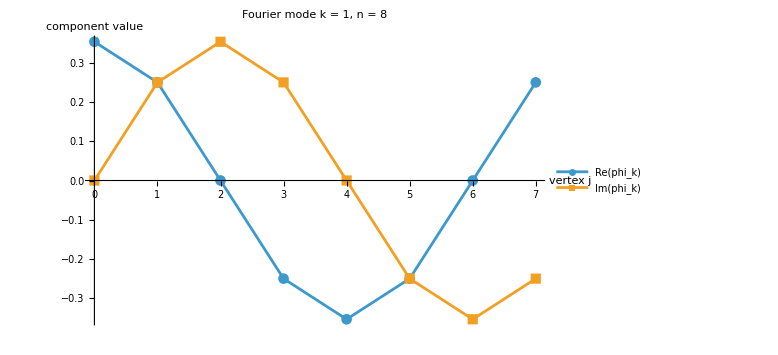

```mathematica
modeComponentPlot[nExample, 1]
```

```mathematica
Manipulate[
  modeComponentPlot[n, k],
  {{n, 8, "dimension"}, 2, 30, 1},
 {{k, 1, "mode"}, Dynamic[Range[0, n - 1]]}
]
```

## 9. The pair-plane

E_(±1)=Span{(φ⃗)_1,(φ⃗)_(n-1)}

A vector in E_(±1) has components

p_j=a ω^j+b ω^-j

```mathematica
pairPlaneVector[n_Integer?Positive, a_, b_] :=
  a fourierVector[n, 1] + b fourierVector[n, n - 1];

pairPlaneCoordinates[p_List] :=
  Transpose[{Re[p], Im[p]}];
```

## 10. Cosine-sine parametrization

After absorbing the common normalization into the coefficients, the components can be written as

p_j=ucos((2πj)/n)+vsin((2πj)/n)

```mathematica
ellipseSample[n_Integer?Positive, a_, b_] :=
  Table[
    (a + b) Cos[2 Pi j/n] + I (a - b) Sin[2 Pi j/n],
    {j, 0, n - 1}
  ];

ellipseIdentityError[n_Integer?Positive, a_, b_] :=
  Max[Abs[N[
    Table[a omega[n]^j + b omega[n]^(-j), {j, 0, n - 1}] -
    ellipseSample[n, a, b]
  ]]];
```

```mathematica
ellipseIdentityError[17, 2 - I, -1/3 + 4 I/5]
```

1.11022×10^-15

## 11. Pair-plane geometry

```mathematica
pairPlanePlot[n_Integer?Positive, a_, b_] := Module[
  {p, pts, curve},
  p = pairPlaneVector[n, a, b];
  pts = pairPlaneCoordinates[p];
  curve = ParametricPlot[
    Evaluate@{
      Re[a Exp[I t] + b Exp[-I t]],
      Im[a Exp[I t] + b Exp[-I t]]
    },
    {t, 0, 2 Pi},
    PlotRange -> All
  ];
  Show[
    curve,
    Graphics[{
      Line[Append[pts, First[pts]]],
      PointSize[0.018],
      Point[pts]
    }],
    Axes -> True,
    AxesLabel -> {"Re", "Im"},
    AspectRatio -> 1,
    ImageSize -> Large
  ]
];
```

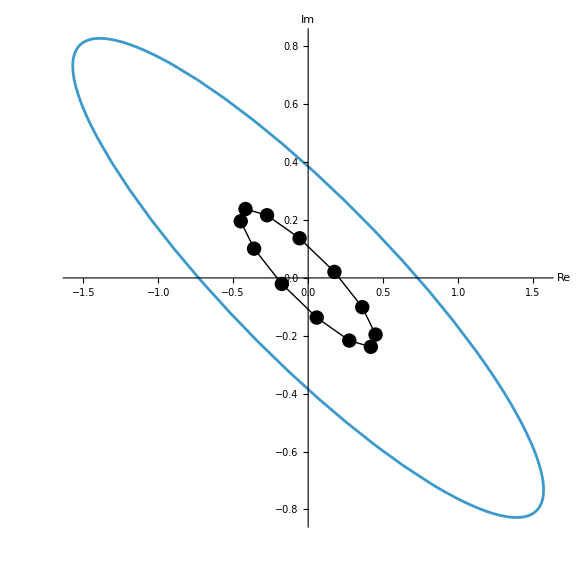

```mathematica
pairPlanePlot[12, 1 + 0.3 I, 0.25 - 0.65 I]
```

```mathematica
Manipulate[
  pairPlanePlot[n, ar + I ai, br + I bi],
  {{n, 12, "number of vertices"}, 3, 40, 1},
  {{ar, 1., "Re(a)"}, -2, 2},
  {{ai, 0.3, "Im(a)"}, -2, 2},
  {{br, 0.25, "Re(b)"}, -2, 2},
  {{bi, -0.65, "Im(b)"}, -2, 2}
]
```

## 12. Degeneracy test

Writing u=a+b and v=i(a-b), the image is a nondegenerate ellipse precisely when u and v are linearly independent as vectors in ℝ^2.

```mathematica
realVector[z_] := {Re[z], Im[z]};

pairPlaneAreaFactor[a_, b_] := Module[{u, v},
  u = a + b;
  v = I (a - b);
  Det[Transpose[{realVector[u], realVector[v]}]]
];

nondegeneratePairPlaneQ[a_, b_, tol_: 10^-10] :=
  Abs[N[pairPlaneAreaFactor[a, b]]] > tol;
```

```mathematica
{
  pairPlaneAreaFactor[1 + 0.3 I, 0.25 - 0.65 I],
  nondegeneratePairPlaneQ[1 + 0.3 I, 0.25 - 0.65 I],
  nondegeneratePairPlaneQ[1, 1]
}
```

{0.605,True,False}

## 13. Automated verification report

```mathematica
Clear[verificationReport];

verificationReport[] := verificationReport[20];

verificationReport[maxN_Integer?Positive] := Module[{rows},
  rows = Table[
    Module[
      {F, gramError, unitaryError, conjugateError, a, b, ellipseError},
      F = fourierMatrix[n];
      gramError = Max[Abs[Flatten[N[
        gramMatrix[n] - IdentityMatrix[n]
      ]]]];
      unitaryError = Max[Abs[Flatten[N[
        ConjugateTranspose[F] . F - IdentityMatrix[n]
      ]]]];
      conjugateError = conjugateModeError[n];
      a = 1 + I/3;
      b = 2/5 - I/4;
      ellipseError = ellipseIdentityError[n, a, b];
      <|
        "n" -> n,
        "Orthonormal basis" -> TrueQ[gramError < 10^-10],
        "Unitary Fourier matrix" -> TrueQ[unitaryError < 10^-10],
        "Conjugate pairing" -> TrueQ[conjugateError < 10^-10],
        "Pair-plane parametrization" -> TrueQ[ellipseError < 10^-10]
      |>
    ],
    {n, 2, maxN}
  ];
  Dataset[rows]
];
```

```mathematica
Length[DownValues[verificationReport]]
```

2

```mathematica
verificationReport[]
```

## Conclusion

The computations verify that the normalized Fourier vectors form an orthonormal basis of ℂ^n, that the Fourier matrix is unitary, and that the pair-plane E_(±1) consists of sampled affine images of the circle.